```mathematica
funcion1:=(r^4+α^2-(r^4+2 r^2 α+3 α^2) f[r]+α (r^2+3 α) f[r]^2-α^2 f[r]^3)/r^2
funcion2:=(2 (3 r^4+α^2)-6 (r^4+r^2 α+α^2) f[r]+3 α (r^2+2 α) f[r]^2-2 α^2 f[r]^3)/(6 r^2)
funcion3:=(r^4+3 α^2-(r^4+4 r^2 α+9 α^2) f[r]+α (2 r^2+9 α) f[r]^2-3 α^2 f[r]^3)/r^2
funcion4:=-((-1+f[r]) (r^4+α^2-2 α^2 f[r]+α^2 f[r]^2))/r^2
```

```mathematica
f1:=f[r]/. Solve[funcion1==μ,f[r],Reals][[1]]
f2:=f[r]/. Solve[funcion2==μ,f[r],Reals][[1]]
f3:=f[r]/. Solve[funcion3==μ,f[r],Reals][[1]]
f4:=f[r]/. Solve[funcion4==μ,f[r],Reals][[1]]
```

```mathematica
a1=α^(n-1)
a2=(α^(n-1))/n
a3=n*α^(n-1)
a4=((1-(-1)^n)/2)*α^(n-1)
```

0.03^(-1+n)

0.03^(-1+n)/n

0.03^(-1+n) n

1/2 0.03^(-1+n) (1-(-1)^n)

```mathematica
Clear[α,μ]
```

```mathematica
α:=0.03
μ:=1
```

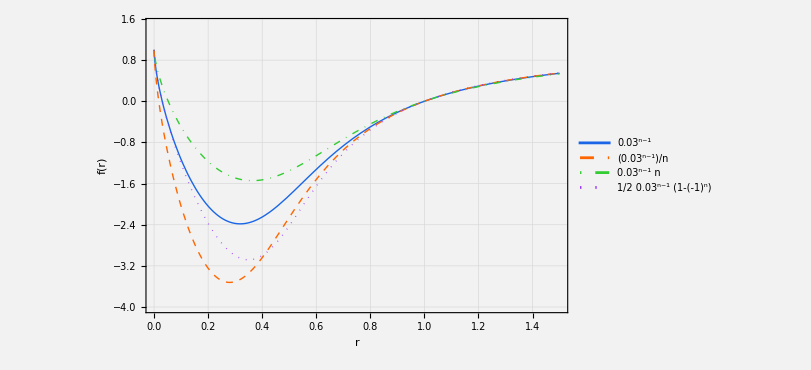

```mathematica
plot1=Plot[{f1,f2,f3,f4},{r,0,1.5},PlotStyle->{{Thick,RGBColor[0.1,0.4,0.9]},(*bright blue*){Thick,Dashed,RGBColor[1,0.4,0]},(*vivid orange*){Thick,DotDashed,RGBColor[0.2,0.8,0.2]},(*bright green*){Thick,Dotted,RGBColor[0.6,0.2,1]}  (*vibrant purple*)},AxesLabel->{"r","f(r)"},LabelStyle->{FontSize->18,Bold,Black},PlotLegends->Placed[{a1,a2,a3,a4},{0.75,0.3}],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.4]],Background->Lighter[Gray,0.9],Frame->True,FrameLabel->{Style["r",Bold,18],Style["f(r)",Bold,18],None,None},FrameStyle->Directive[Black,Thick],ImageSize->600,PlotRange->{-4,1.5},BaseStyle->{FontFamily->"Helvetica",FontSize->16},PlotTheme->"Detailed"]
```

```mathematica
Export["plo1.png",plot1]
```

plo1.png